--- SCENARIO 5: Exact Numerical Solution (NDSolve) ---

(Simulating the Dzhanibekov flip dynamically for 20 seconds)

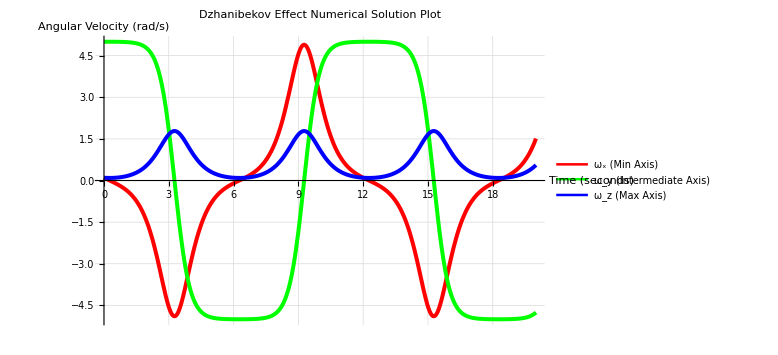

```mathematica
FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]];
ClearAll["Global`*"];

(*NUMERIC PARAMETERS (Moments of Inertia)*)
I1Num=8.314;   (*Minimum Axis*)
I2Num=10.065;  (*Intermediate Axis-The axis where the flip occurs*)
I3Num=16.664;  (*Maximum Axis*)

(*EXACT NUMERIC INITIAL CONDITIONS (Angular Velocities at t=0)*)
w1Num=0.1;
w2Num=5.0;
w3Num=0.1;

(*EULER EQUATIONS WITH NUMERICAL VALUES*)
eq1Num=I1Num*w1'[t]==(I2Num-I3Num)*w2[t]*w3[t];
eq2Num=I2Num*w2'[t]==(I3Num-I1Num)*w3[t]*w1[t];
eq3Num=I3Num*w3'[t]==(I1Num-I2Num)*w1[t]*w2[t];

(*Numerical initial condition equalities*)
init1Num=w1[0]==w1Num;
init2Num=w2[0]==w2Num;
init3Num=w3[0]==w3Num;

Print["--- SCENARIO 5: Exact Numerical Solution (NDSolve) ---"];
Print["(Simulating the Dzhanibekov flip dynamically for 20 seconds)"];

(*NUMERICAL SOLVER (NDSolve)*)
(*NDSolve calculates the exact path step-by-step,providing interpolating functions.*)
(*Semicolon (;) at the end to suppress the raw function output.*)
numericalSolution=NDSolve[{eq1Num,eq2Num,eq3Num,init1Num,init2Num,init3Num},{w1,w2,w3},{t,0,20}];

(*PLOTTING THE RESULT*)
(*Evaluate forces the plot to use the solved interpolating functions.*)
Plot[Evaluate[{w1[t],w2[t],w3[t]}/. numericalSolution],{t,0,20},PlotStyle->{{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotLegends->{"\!\(\*SubscriptBox[\(ω\), \(x\)]\) (Min Axis)","\!\(\*SubscriptBox[\(ω\), \(y\)]\) (Intermediate Axis)","\!\(\*SubscriptBox[\(ω\), \(z\)]\) (Max Axis)"},AxesLabel->{"Time (seconds)","Angular Velocity (rad/s)"},PlotLabel->"Dzhanibekov Effect Numerical Solution Plot",GridLines->Automatic,ImageSize->Large]
```